```mathematica
stepGradient[func_,start_,λ_,steps_,vars_]:=stepGradient[func,start,λ,steps,vars]=Module[{},
vals={start};
grd[f_,v_][n_]:=Grad[f,v]/.Thread[v->n];
grad=grd[func,vars];
Print[grad[{m,b}]];
For[i=0,i<steps,i++,
vals={vals,(Last@vals)-λ*grad[Last@vals]}
];
Cases[vals,{__},{-2}]
];
```

```mathematica
f[x_,y_]:=Sin[1/2x^2-1/4y^2+3]Cos[2x+1-Exp[y]]

width=5;
height=5;

Manipulate[
DynamicModule[{},
points2D=stepGradient[g[x,y],Setting@Dynamic@start,λ,numPoints,{x,y}];
points3D=(Append[#,g@@#]&)/@points2D;
p1=Show[
Plot3D[g[x,y],{x,-width/2,width/2},{y,-height/2,height/2},ColorFunction->"Rainbow"],
Graphics3D[{Thickness[0.005],Red,Line[points3D]}],
Graphics3D[{PointSize[0.02],Red,Point[points3D]}],
ImageSize->Large
];
p2=LocatorPane[Dynamic@start,Show[{ContourPlot[g[x,y],{x,-width/2,width/2},{y,-height/2,height/2},ColorFunction->"Rainbow"],Graphics[{Thick,Red,Line[points2D]}],
Graphics[{PointSize[0.02],Red,Point[points2D]}]},ImageSize->Medium], LocatorAutoCreate->False,ContinuousAction->False];
Row[{p1,Dynamic@p2}]
],
{{g,f,"Function"},{f->"Terrain",(Sin[#1]Cos[#2]&)->"Hills",(#1^2+#2^2&)->"Paraboloid", (error/.m->#1/.b->#2&)->"Error"}},
{{numPoints,2,"Number of Iterations"},1,25,1},
{{λ,0.2,"Weight"},0.01,1,0.01},
{{start,{-0.34,-2}},None},
ContinuousAction->False
]
```

{1/30 (-198.332 (3.37982-b-99.1662 m)-187.512 (7.30174-b-93.7559 m)-177.34 (7.25821-b-88.67 m)-176.716 (8.53945-b-88.358 m)-175.591 (18.1405-b-87.7953 m)-173.854 (24.7838-b-86.9271 m)-160.816 (26.9515-b-80.4082 m)-153.42 (17.7702-b-76.7098 m)-153.118 (27.7427-b-76.5588 m)-138.275 (37.1924-b-69.1377 m)-131.663 (56.2507-b-65.8313 m)-121.654 (39.9823-b-60.8268 m)-106.02 (28.4199-b-53.0101 m)-105.487 (22.6586-b-52.7435 m)-97.2859 (54.3052-b-48.6429 m)-85.8466 (62.2913-b-42.9233 m)-81.2818 (46.1734-b-40.6409 m)-80.5592 (37.7958-b-40.2796 m)-73.9133 (80.688-b-36.9566 m)-65.0649 (42.6906-b-32.5325 m)-64.543 (65.0495-b-32.2715 m)-42.3555 (87.3434-b-21.1777 m)-30.0704 (90.0622-b-15.0352 m)-27.2459 (79.9802-b-13.623 m)-19.6144 (87.0357-b-9.80719 m)-18.4647 (92.1588-b-9.23237 m)-17.2389 (59.9636-b-8.61945 m)-15.1266 (95.4536-b-7.56329 m)-13.6495 (79.1414-b-6.82476 m)-8.9599 (95.2931-b-4.47995 m)),1/30 (-2 (3.37982-b-99.1662 m)-2 (7.30174-b-93.7559 m)-2 (7.25821-b-88.67 m)-2 (8.53945-b-88.358 m)-2 (18.1405-b-87.7953 m)-2 (24.7838-b-86.9271 m)-2 (26.9515-b-80.4082 m)-2 (17.7702-b-76.7098 m)-2 (27.7427-b-76.5588 m)-2 (37.1924-b-69.1377 m)-2 (56.2507-b-65.8313 m)-2 (39.9823-b-60.8268 m)-2 (28.4199-b-53.0101 m)-2 (22.6586-b-52.7435 m)-2 (54.3052-b-48.6429 m)-2 (62.2913-b-42.9233 m)-2 (46.1734-b-40.6409 m)-2 (37.7958-b-40.2796 m)-2 (80.688-b-36.9566 m)-2 (42.6906-b-32.5325 m)-2 (65.0495-b-32.2715 m)-2 (87.3434-b-21.1777 m)-2 (90.0622-b-15.0352 m)-2 (79.9802-b-13.623 m)-2 (87.0357-b-9.80719 m)-2 (92.1588-b-9.23237 m)-2 (59.9636-b-8.61945 m)-2 (95.4536-b-7.56329 m)-2 (79.1414-b-6.82476 m)-2 (95.2931-b-4.47995 m))}

{1.05092×10^22,1.54988×10^20}

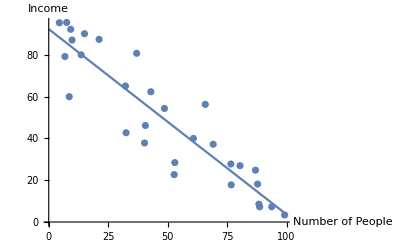

```mathematica
listSize=30;
listMax=100;
dist[rho_]:=CopulaDistribution[{"Binormal",rho},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}];
list=listMax*RandomVariate[dist[-.95],listSize];

error=1/listSize*Sum[(Last@list[[i]]-(m*First@list[[i]]+b))^2,{i,1,listSize}];

steps=stepGradient[error,{-1,listMax},0.05,10,{m,b}];
{mf,bf}=Last@steps
bestFit=Fit[list,{1,x},x];
Show[ListPlot[list,AxesLabel->{"Number of People","Income"}],Plot[mf*x+bf,{x,0,listMax}],Plot[bestFit,{x,0,listMax}]]
```